# H_2 dynamics: recompilation vs Trotter

```mathematica
SetEnvironment["OMP_NUM_THREADS"->"8"]
```

```mathematica
Import["https://qtechtheory.org/questlink.m"];
SetDirectory[NotebookDirectory[]];
CreateLocalQuESTEnv["quest_link_cpu"];
```

## modules

```mathematica
FormatHamiltonian::usage="Format the hamiltonian from qiskit;daniel's format";
FormatHamiltonian[filename_]:=Module[{stringham,ham,nterms,nqubits,a},
stringham=Import[filename];
ham=ToExpression[stringham]/.{{a_?NumberQ}->{a Subscript[Id, 0]}};
nqubits=1+Select[Flatten[Level[#,-1]&/@Flatten@ham],NumericQ[#]&]//Max;
nterms=Length@ham;
{Total@Apply[Times,ham,1],nterms,nqubits}
]

GetBlocks::usage="GetBlocks[blockdiagmat_,draw_:True]. Partition indices of a matrix by its blocks.";
GetBlocks[mat_,draw_:True]:=Module[{adjmat,dim=Length@mat,graph},
adjmat=ConstantArray[0,{dim,dim}];
Table[adjmat⟦i,j⟧=If[mat⟦i,j⟧==0,0,1],{i,dim},{j,dim}];
graph=AdjacencyGraph@adjmat;
If[draw,Print@graph];
ConnectedComponents@graph-1
]
```

```mathematica
MatrixDist::usage="MatrixDist[matrix1, matrix2, subspace, plotglobalphase:False]. Calculate distance of 2 matrices by formula: 
                                    max_λ |Π_S(U-V)Π_S| 
                    namely, maximum absolute eigenvalues of the matrix difference projected to the subspace of interest.";
MatrixDist[M1_,M2_,subspace_,plotglobalphase_:False]:=Module[{sm1,sm2,globalphase,mindist,F,ϕ},
{sm1,sm2}=If[Length@subspace<Length@M1,{GetSubMatrix[M1,subspace],GetSubMatrix[M2,subspace]},{M1,M2}];
F[ϕ_?NumericQ]:=Max[Re@Sqrt[Abs@Eigenvalues[GetSubMatrix[ConjugateTranspose[M1-Exp[ⅈ*ϕ]M2].(M1-Exp[ⅈ*ϕ]*M2),subspace]]]];
{mindist,globalphase}=NMinimize[{F[ϕ],0≤ϕ<2π},ϕ,PrecisionGoal->5,MaxIterations->1000];
If[plotglobalphase,Print@DiscretePlot[F[ϕ],{ϕ,0,2π,0.01},AxesLabel->{"ϕ","max_λ |Π_S(U-ⅇ^ⅈϕV)Π_S|"},PlotLabel->ToString@subspace]];
{mindist,ϕ/.globalphase}
]

GetSubMatrix::usage="GetSubMatrix[matrix,subspace]. Return the submatrix in the subspace.";
GetSubMatrix[matrix_,subspace_ ]:=Module[{sm,dim,x=0,y=0},
dim=Length@subspace;
sm=IdentityMatrix[dim];
Table[
++x;y=0;
Table[
++y;
sm⟦x,y⟧=matrix⟦s+1,ss+1⟧;
,{ss,subspace}]
,{s,subspace}];
sm
]

SetAttributes[CompileMe,HoldAll]
CompileMe[nq_,matrix_,conf_,printmatrices_:False]:=Module[{ψ,ψinit,dist,cost,globalphase},
{runtime,{costlist,ansatz,θvars,finmsg,ncycle,fev,aborted,cycleres,elim}}=AbsoluteTiming[CJRecompile[nq,matrix,conf]];
Print[{ansatz,θvars,aborted,fev,ncycle,"{merged, θsmall, metric, bruteforce}=",elim,finmsg}];
(*
Print[ListPlot[costlist,PlotRange->All,Joined->True,PlotMarkers->{Automatic,None},PlotLegends->{"<E>","Ground state"}]];
*)
Print[DrawCircuit[ansatz,nq]];
Print["cost=",Last@costlist,"; ngates=",Length@ansatz];
Print["runtime= ",runtime/60," minutes"];

(*sanity check*)
{ψ,ψinit}=CreateQuregs[conf["nqubit"],2];
PrepareInitState[conf,InitZeroState@ψinit];
ApplyCircuit[CloneQureg[ψ,ψinit],{Subscript[U, Sequence@Range[0,conf["nqubit"]-1]][KroneckerProduct[IdentityMatrix[2^conf["nqancilla"]],matrix]]}];
ApplyCircuit[ψ,ansatz/.CustomGatesDefinitions/.θvars];
cost=CostFidelity[ψ,ψinit];
If[(cost-Last@costlist)>10^-13,
Print["WARNIG:didn't pass sanity check"];
Print["error=",cost-Last@costlist]
];
DestroyAllQuregs[];

vmat=ConjugateTranspose@CalcCircuitMatrix[ansatz/.CustomGatesDefinitions/.θvars,nq];
{dist,globalphase}=MatrixDist[matrix,vmat,conf["subspace"]];
Print["cost=",cost, " ;dist=",dist, "; globalphase=",globalphase];
If[printmatrices,
Print@MatrixForm@Chop@GetSubMatrix[matrix,conf["subspace"]];
Print@MatrixForm@Chop@GetSubMatrix[Exp[ⅈ*globalphase]vmat,conf["subspace"]];
];
{cost,dist,Length@ansatz,runtime/60,ansatz,θvars,cycleres}
]
```

```mathematica
BlockByOccupation::usage="BlockByOccupation[nqubits, occupation_number], return a block that has the correct occupation number";
BlockByOccupation[nqubits_,occnum_]:=Select[Range[0,2^nqubits-1],DigitCount[#,2,1]==occnum&]
```

```mathematica
BlockBySpin::usage="BlockBySpin[spin_hamiltonian, expected_spin, nqubits], return a block that has the correct occupation number";
BlockBySpin[spinham_,spin_,nqubits_]:=Module[{ψ,ψwork,blocks,circ,j},
{ψ,ψwork}=CreateQuregs[nqubits,2];
blocks=Table[
blocks=(Reverse@Flatten@Position[Reverse@IntegerDigits[i,2,nqubits],1]-1 )/.j_Integer->Subscript[X, j];
If[Length@circ>0,ApplyCircuit[InitZeroState@ψ,circ]];
If[Abs[CalcExpecPauliSum[ψ,spinham,ψwork]-spin]≤10^-13,i,{}]
,{i,0,2^nqubits-1}];
DestroyQureg[ψ];
DestroyQureg[ψwork];
Flatten@blocks
]
```

## Hamiltonian generation

```mathematica
{hamiltonian,nterms,nqubits}=FormatHamiltonian["~/vqe/molecules/H2/H2.txt"]
```

{-0.0970663 Id_0-0.0453026 X_2 X_3 Y_0 Y_1+0.0453026 X_0 X_3 Y_1 Y_2+0.0453026 X_1 X_2 Y_0 Y_3-0.0453026 X_0 X_1 Y_2 Y_3+0.171413 Z_0+0.171413 Z_1+0.168689 Z_0 Z_1-0.223432 Z_2+0.120625 Z_0 Z_2+0.165928 Z_1 Z_2-0.223432 Z_3+0.165928 Z_0 Z_3+0.120625 Z_1 Z_3+0.174413 Z_2 Z_3,15,4}

```mathematica
{spin,nterms,nqubits}=FormatHamiltonian["~/vqe/molecules/H2/spin.txt"];
```

```mathematica
hammat=CalcPauliSumMatrix@hamiltonian;
```

## All data and the processing

### Load data and raw data

Compilation in the subspace and full space

Raw data

```mathematica
ressubH2<<ressubH2.mx;
resfullH2<<resfullH2.mx;
```

Processed data

```mathematica
subcompsum<<subcompsum.mx;
fullcompsum<<fullcompsum.mx;
```

Trotterization with distance in the subspace and full space

{{twos,singles},distance,entFid,<E(t)>err,Fiderr of psi(t)}

```mathematica
trotsumsub<<trotsumsub.mx;
trotsum<<trotsum.mx;
```

Table[
 Print["t=", t];
 Print@Row[{TableForm@Table[{res[[2]], res[[3]]}, {res, ressubH2[t]}], "      ", TableForm@Table[{res[[2]], res[[3]]}, {res, resfullH2[t]}]}]
 , {t, times}]

Distance to identity matrix in the subspace

```mathematica
Complement[Keys@ressubH2,Keys@trotsumsub]
```

{0.35,3.3,3.7,4.3,4.5}

```mathematica
Keys@subcompsum
Keys@fullcompsum
```

{0.001,0.01,0.1,1,4,0.005,0.05,0.5,2,0.002,0.035,0.007,0.02,0.03,0.07,0.15,0.25,0.3,0.4,0.6,0.75,0.9,1.1,1.2,1.35,1.5,1.65,1.8,2.2,2.35,2.55,2.85,3,3.5,3.3,3.7,4.3,4.5,0.35}

{0.001,0.01,0.1,1,4,0.005,0.05,0.5,2,0.002,0.035,0.007,0.02,0.03,0.07,0.15,0.25,0.3,0.4,0.6,0.75,0.9,1.1,1.2,1.35,1.5,1.65,1.8,2.2,2.35,2.55,2.85,3,3.5,3.3,3.7,4.3,4.5,0.35}

```mathematica
times=Sort@Keys@subcompsum
subspace={3,5,6,9,10,12}
```

{0.001,0.002,0.005,0.007,0.01,0.02,0.03,0.035,0.05,0.07,0.1,0.15,0.25,0.3,0.35,0.4,0.5,0.6,0.75,0.9,1,1.1,1.2,1.35,1.5,1.65,1.8,2,2.2,2.35,2.55,2.85,3,3.3,3.5,3.7,4,4.3,4.5}

{3,5,6,9,10,12}

distidsub=<|ParallelTable[t->MatrixDist[MatrixExp[-ⅈ t hammat],IdentityMatrix[2^nqubits],subspace][[1]],{t,times}]|>;

DumpSave["distidsub.mx", distidsub];

Distance to identity matrix: full space optimization, full space optimization for subspace dist, and subspace-optimized

```mathematica
times
```

{0.001,0.002,0.005,0.007,0.01,0.02,0.03,0.035,0.05,0.07,0.1,0.15,0.25,0.3,0.35,0.4,0.5,0.6,0.75,0.9,1,1.1,1.2,1.35,1.5,1.65,1.8,2,2.2,2.35,2.55,2.85,3,3.3,3.5,3.7,4,4.3,4.5}

```mathematica
ts=Sort@DeleteDuplicates@Join[N@Subdivide[0.01,20,311],N@times]
Length@ts
```

{0.001,0.002,0.005,0.007,0.01,0.02,0.03,0.035,0.05,0.07,0.0742765,0.1,0.138553,0.15,0.20283,0.25,0.267106,0.3,0.331383,0.35,0.395659,0.4,0.459936,0.5,0.524212,0.588489,0.6,0.652765,0.717042,0.75,0.781318,0.845595,0.9,0.909871,0.974148,1.,1.03842,1.1,1.1027,1.16698,1.2,1.23125,1.29553,1.35,1.35981,1.42408,1.48836,1.5,1.55264,1.61691,1.65,1.68119,1.74547,1.8,1.80974,1.87402,1.9383,2.,2.00257,2.06685,2.13113,2.1954,2.2,2.25968,2.32395,2.35,2.38823,2.45251,2.51678,2.55,2.58106,2.64534,2.70961,2.77389,2.83817,2.85,2.90244,2.96672,3.,3.031,3.09527,3.15955,3.22383,3.2881,3.3,3.35238,3.41666,3.48093,3.5,3.54521,3.60949,3.67376,3.7,3.73804,3.80232,3.86659,3.93087,3.99514,4.,4.05942,4.1237,4.18797,4.25225,4.3,4.31653,4.3808,4.44508,4.5,4.50936,4.57363,4.63791,4.70219,4.76646,4.83074,4.89502,4.95929,5.02357,5.08785,5.15212,5.2164,5.28068,5.34495,5.40923,5.4735,5.53778,5.60206,5.66633,5.73061,5.79489,5.85916,5.92344,5.98772,6.05199,6.11627,6.18055,6.24482,6.3091,6.37338,6.43765,6.50193,6.56621,6.63048,6.69476,6.75904,6.82331,6.88759,6.95186,7.01614,7.08042,7.14469,7.20897,7.27325,7.33752,7.4018,7.46608,7.53035,7.59463,7.65891,7.72318,7.78746,7.85174,7.91601,7.98029,8.04457,8.10884,8.17312,8.2374,8.30167,8.36595,8.43023,8.4945,8.55878,8.62305,8.68733,8.75161,8.81588,8.88016,8.94444,9.00871,9.07299,9.13727,9.20154,9.26582,9.3301,9.39437,9.45865,9.52293,9.5872,9.65148,9.71576,9.78003,9.84431,9.90859,9.97286,10.0371,10.1014,10.1657,10.23,10.2942,10.3585,10.4228,10.4871,10.5514,10.6156,10.6799,10.7442,10.8085,10.8727,10.937,11.0013,11.0656,11.1298,11.1941,11.2584,11.3227,11.3869,11.4512,11.5155,11.5798,11.6441,11.7083,11.7726,11.8369,11.9012,11.9654,12.0297,12.094,12.1583,12.2225,12.2868,12.3511,12.4154,12.4796,12.5439,12.6082,12.6725,12.7368,12.801,12.8653,12.9296,12.9939,13.0581,13.1224,13.1867,13.251,13.3152,13.3795,13.4438,13.5081,13.5723,13.6366,13.7009,13.7652,13.8295,13.8937,13.958,14.0223,14.0866,14.1508,14.2151,14.2794,14.3437,14.4079,14.4722,14.5365,14.6008,14.665,14.7293,14.7936,14.8579,14.9222,14.9864,15.0507,15.115,15.1793,15.2435,15.3078,15.3721,15.4364,15.5006,15.5649,15.6292,15.6935,15.7577,15.822,15.8863,15.9506,16.0149,16.0791,16.1434,16.2077,16.272,16.3362,16.4005,16.4648,16.5291,16.5933,16.6576,16.7219,16.7862,16.8505,16.9147,16.979,17.0433,17.1076,17.1718,17.2361,17.3004,17.3647,17.4289,17.4932,17.5575,17.6218,17.686,17.7503,17.8146,17.8789,17.9432,18.0074,18.0717,18.136,18.2003,18.2645,18.3288,18.3931,18.4574,18.5216,18.5859,18.6502,18.7145,18.7787,18.843,18.9073,18.9716,19.0359,19.1001,19.1644,19.2287,19.293,19.3572,19.4215,19.4858,19.5501,19.6143,19.6786,19.7429,19.8072,19.8714,19.9357,20.}

350

Distance to identity matrix : full space optimization, full space optimization for subspace dist, and subspace - optimized

```mathematica
distToID[hammat_,t_,subspace_]:=Module[{M1,M2,globalphase,mindist,fullopt,subopt,fullsubopt,dsubopt,dfullopt,dfullsubopt,ϕ,dynmat},
M1=MatrixExp[-ⅈ t hammat];
M2=IdentityMatrix[Length@M1];

subopt[ϕ_?NumericQ]:=Max[Re@Sqrt[Abs@Eigenvalues[GetSubMatrix[ConjugateTranspose[M1-Exp[ⅈ*ϕ]M2].(M1-Exp[ⅈ*ϕ]*M2),subspace]]]];
fullopt[ϕ_?NumericQ]:=Max[Re@Sqrt[Abs@Eigenvalues[ConjugateTranspose[M1-Exp[ⅈ*ϕ]M2].(M1-Exp[ⅈ*ϕ]*M2)]]];
fullsubopt[ϕ_?NumericQ]:=Max[Re[Sqrt[Abs@Eigenvalues[ConjugateTranspose[M1-Exp[ⅈ*ϕ]M2].(M1-Exp[ⅈ*ϕ]*M2)]]][[1+subspace]]];

{dsubopt,globalphase}=NMinimize[{subopt[ϕ],0≤ϕ<2π},ϕ,PrecisionGoal->5,MaxIterations->1000];
{dfullsubopt,globalphase}=NMinimize[{fullsubopt[ϕ],0≤ϕ<2π},ϕ,PrecisionGoal->5,MaxIterations->1000];
{dfullopt,globalphase}=NMinimize[{fullopt[ϕ],0≤ϕ<2π},ϕ,PrecisionGoal->5,MaxIterations->1000];

<|"fullopt"->dfullopt,"subopt"->dsubopt,"fullsubopt"->dfullsubopt|>
]
```

```mathematica
disttoid=ParallelTable[]
```

DumpSave["distidfull.mx", distidfull];

```mathematica
distid<<distid.mx;
distidfull<<distidfull.mx;
```

```mathematica
Complement[subcompsum//Keys,distid//Keys]
```

{0.007,0.035,0.3,0.35,0.6,0.75,1.1,1.2,1.35,1.65,1.8,2.2,2.35,2.55,2.85,3.3,3.7,4.3}

```mathematica
Keys@distid//Length
{0.007,0.035,0.3,0.35,0.6,0.75,1.1,1.2,1.35,1.65,1.8,2.2,2.35,2.55,2.85,3.3,3.7,4.3}
```

424

{0.007,0.035,0.3,0.35,0.6,0.75,1.1,1.2,1.35,1.65,1.8,2.2,2.35,2.55,2.85,3.3,3.7,4.3}

### Load data

Get best results with distance at least 0.001 (subspace distance) from recompilation

```mathematica
times={0.001,0.01,0.1,1,4,0.005,0.05,0.5,2,0.002,0.02,0.03,0.07,0.15,0.25,0.3,0.4,0.6,0.75,0.9,1.1,1.2,1.35,1.5,1.65,1.8,2.2,2.35,2.55,2.85,3,3.5,3.3,3.7,4.3,4.5,0.35}
```

{0.001,0.01,0.1,1,4,0.005,0.05,0.5,2,0.002,0.02,0.03,0.07,0.15,0.25,0.3,0.4,0.6,0.75,0.9,1.1,1.2,1.35,1.5,1.65,1.8,2.2,2.35,2.55,2.85,3,3.5,3.3,3.7,4.3,4.5,0.35}

```mathematica
mindist=1*10^-3;
bestsub=<|Table[t->First@MinimalBy[MinimalBy[Select[subcompsum[t],#["distsub"]<=mindist&],Length[#["ansatz"]]&],#["distsub"]&],{t,Keys@subcompsum}]|>;
bestfull=<|Table[t->First@MinimalBy[MinimalBy[Select[fullcompsum[t],#["distsub"]<=mindist&],Length[#["ansatz"]]&],#["distsub"]&],{t,Keys@fullcompsum}]|>;
(*indicate the fail results*)
Print["failed runs on fullspace-compiled for Δt:",Select[bestfull,Length@#===1&]//Keys];
Print["failed runs on subspace-compiled for Δt:",Select[bestsub,Length@#===1&]//Keys];


(*select the successfull results only*)
bestsub=Select[bestsub,Length@#>1&];
bestfull=Select[bestfull,Length@#>1&];
```

First::nofirst: {} has zero length and no first element.

failed runs on fullspace-compiled for Δt:{0.035,0.007}

failed runs on subspace-compiled for Δt:{}

All Trotter results with at distance at most 0.001 (subspace and full-space distances)

```mathematica
tbestsub=<|Table[t->Select[Flatten[Values[trotsumsub[t]],1],#[[2]]<=mindist&],{t,Keys@trotsumsub}]|>;
tbestfull=<|Table[t->Select[Flatten[Values[trotsum[t]],1],#[[2]]<=mindist&],{t,Keys@trotsum}]|>;
```

```mathematica
besttrotsub=<|Table[t->First@MinimalBy[MinimalBy[Select[{Total@#[[1]],#[[2]]}&/@Flatten[Values@trotsumsub[t],1],#[[2]]<=mindist&],#[[1]]&],#[[2]]&],{t,Keys@trotsumsub}]|>;
besttrotfull=<|Table[t->First@MinimalBy[MinimalBy[Select[{Total@#[[1]],#[[2]]}&/@Flatten[Values@trotsum[t],1],#[[2]]<=mindist&],#[[1]]&],#[[2]]&],{t,Keys@trotsum}]|>;
```

Pick the closest distance of trotterization with minimal number of gates
subspace-recompiled vs trotterization with subspace distance

```mathematica
datacompfull=With[{m=Max[Length[#]&/@bestfull⟦All,"ansatz"⟧]},Table[{t,Length@bestfull[t]["ansatz"]},{t,Keys@bestfull}]/.{{d_,m}->Labeled[{d,m},m,Background->None]}]
datacompsub=With[{m=Max[Length[#]&/@bestsub⟦All,"ansatz"⟧]},Table[{t,Length@bestsub[t]["ansatz"]},{t,Keys@bestsub}]/.{{d_,m}->Labeled[{d,m},m,Background->None]}]
datatrotsub=With[{m=Max[besttrotsub⟦All,1⟧]},Table[{t,Total@besttrotsub[t][[1]]},{t,Keys@besttrotsub}]/.{{d_,m}->Labeled[{d,m},m,Background->None]}]
datatrotfull=With[{m=Max[besttrotfull⟦All,1⟧]},Table[{t,Total@besttrotfull[t][[1]]},{t,Keys@besttrotfull}]/.{{d_,m}->Labeled[{d,m},m,Background->None]}]
```

{{0.001,6},{0.01,23},{0.1,28},{1,30},{4,34}34,{0.005,19},{0.05,30},{0.5,28},{2,31},{0.002,13},{0.02,26},{0.03,28},{0.07,26},{0.15,24},{0.25,28},{0.3,23},{0.4,24},{0.6,26},{0.75,25},{0.9,31},{1.1,30},{1.2,30},{1.35,29},{1.5,31},{1.65,29},{1.8,27},{2.2,29},{2.35,26},{2.55,28},{2.85,29},{3,29},{3.5,29},{3.3,33},{3.7,28},{4.3,32},{4.5,33},{0.35,22}}

{{0.001,2},{0.01,14},{0.1,15},{1,16},{4,18}18,{0.005,5},{0.05,12},{0.5,17},{2,16},{0.002,13},{0.035,12},{0.007,16},{0.02,14},{0.03,16},{0.07,17},{0.15,14},{0.25,16},{0.3,14},{0.4,14},{0.6,16},{0.75,16},{0.9,16},{1.1,17},{1.2,15},{1.35,15},{1.5,15},{1.65,17},{1.8,16},{2.2,17},{2.35,17},{2.55,17},{2.85,17},{3,16},{3.5,15},{3.3,18}18,{3.7,18}18,{4.3,17},{4.5,16},{0.35,16}}

{{0.001,78},{0.005,78},{0.01,78},{0.05,78},{0.1,152},{1,468},{2,936},{4,1170}1170,{0.002,78},{0.035,78},{0.007,78},{0.02,78},{0.03,78},{0.07,78},{0.15,152},{0.25,152},{0.5,234},{0.3,234},{0.4,234},{0.6,234},{0.75,386},{0.9,468},{1.1,468},{1.2,468},{1.35,702},{1.5,702},{1.65,702},{1.8,702},{2.2,936},{2.35,936},{2.55,1088},{2.85,1170}1170,{3,1170}1170,{3.5,1170}1170}

{{0.001,78},{0.005,78},{0.01,78},{0.05,78},{0.1,152},{1,468},{2,936},{4,1170}1170,{0.002,78},{0.035,78},{0.007,78},{0.02,78},{0.03,78},{0.07,78},{0.15,152},{0.25,152},{0.5,234},{0.3,234},{0.4,234},{0.6,234},{0.75,386},{0.9,468},{1.1,468},{1.2,468},{1.35,702},{1.5,702},{1.65,702},{1.8,702},{2.2,936},{2.35,936},{2.55,1088},{2.85,1170}1170,{3,1170}1170,{3.5,1170}1170}

### Plot the best results on every methode

```mathematica
rainbowcol[n_]:=Table[ColorData["Rainbow",(i-1)/n],{i,n}]
```

```mathematica
style[ndata_,legends_,legendpos_]:={AspectRatio->2/3,ImageSize->400,
LabelStyle->{FontFamily->"FreeSerif",FontSize->15,Background->None},Frame->True,FrameTicks->Automatic,FrameStyle->Directive[Black,18,FontFamily->"FreeSerif"],
PlotStyle->Reverse@rainbowcol[ndata],PlotMarkers->{Automatic,.02},Background->White,PlotLegends->Placed[PointLegend[Automatic,legends,Spacings->0.,LegendFunction->(Framed[#,FrameStyle->(Antialiasing->False),FrameMargins->0,Background->White]&)],
legendpos],PlotRange->All,GridLinesStyle->Directive[Black, Dashed]};
```

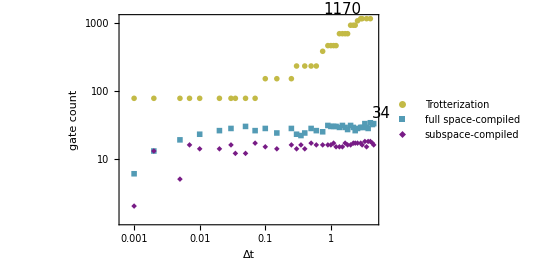

```mathematica
ListLogLogPlot[{datatrotsub,datacompfull,datacompsub},FrameLabel->{"Δt","gate count"},GridLines->{None, {18,34,1170}},style[3,{"Trotterization","full space-compiled","subspace-compiled"},{0.7,0.15}]]
```

```mathematica
hammat=CalcPauliSumMatrix[hamiltonian];subspace={3,5,6,9,10,12};
```

```mathematica
besttrotsub
```

<|0.001→{78,1.431×10^-7},0.005→{78,3.57749×10^-6},0.01→{78,0.0000143099},0.05→{78,0.000357684},0.1→{152,0.0000378907},1→{468,0.000387835},2→{936,0.000536372},4→{1170,0.000785579},0.002→{78,5.72399×10^-7},0.035→{78,0.000175282},0.007→{78,7.01187×10^-6},0.02→{78,0.0000572383},0.03→{78,0.000128781},0.07→{78,0.000700939},0.15→{152,0.000127777},0.25→{152,0.000590029},0.5→{234,0.000210902},0.3→{234,0.0000273976},0.4→{234,0.0000865019},0.6→{234,0.000436583},0.75→{386,0.000787236},0.9→{468,0.000258813},1.1→{468,0.000557176},1.2→{468,0.000772751},1.35→{702,0.000345294},1.5→{702,0.00050238},1.65→{702,0.000697876},1.8→{702,0.000931715},2.2→{936,0.000704111},2.35→{936,0.000835337},2.55→{1088,0.000978671},2.85→{1170,0.000605165},3→{1170,0.000633994},3.5→{1170,0.00059477}|>

```mathematica
datacompsub2=With[{m=Max[Length[#]&/@bestsub⟦All,"ansatz"⟧]},Table[{distidsub[t],Length@bestsub[t]["ansatz"]},{t,times}]];
datatrotsub2=With[{m=Max[besttrotsub⟦All,1⟧]},Table[{distidsub[t],Total@besttrotsub[t]},{t,times}]]
```

{{0.000810213,78.},{0.00162043,78.},{0.00405106,78.},{Missing[KeyAbsent,0.007],78.},{0.00810211,78.},{0.0162041,78.0001},{0.0243058,78.0001},{Missing[KeyAbsent,0.035],78.0002},{0.0405079,78.0004},{0.0567073,78.0007},{0.0809992,152.},{0.121457,152.},{0.202207,152.001},{Missing[KeyAbsent,0.3],234.},{Missing[KeyAbsent,0.35],Total[Missing[KeyAbsent,0.35]]},{0.322669,234.},{0.402342,234.},{Missing[KeyAbsent,0.6],234.},{Missing[KeyAbsent,0.75],386.001},{0.713144,468.},{0.788234,468.},{Missing[KeyAbsent,1.1],468.001},{Missing[KeyAbsent,1.2],468.001},{Missing[KeyAbsent,1.35],702.},{1.1419,702.001},{Missing[KeyAbsent,1.65],702.001},{Missing[KeyAbsent,1.8],702.001},{1.44887,936.001},{Missing[KeyAbsent,2.2],936.001},{Missing[KeyAbsent,2.35],936.001},{Missing[KeyAbsent,2.55],1088.},{Missing[KeyAbsent,2.85],1170.},{1.76596,1170.},{Missing[KeyAbsent,3.3],Total[Missing[KeyAbsent,3.3]]},{1.68374,1170.},{Missing[KeyAbsent,3.7],Total[Missing[KeyAbsent,3.7]]},{1.64856,1170.},{Missing[KeyAbsent,4.3],Total[Missing[KeyAbsent,4.3]]},{1.81781,Total[Missing[KeyAbsent,4.5]]}}

```mathematica
ListPlot[
{datatrotsub2,datacompsub2},GridLines->None,PlotLegends->Placed[PointLegend[Automatic,{"Trotterization","subspace compilation","subspace compilation"},Spacings->0.,LegendFunction->(Framed[#,FrameStyle->(Antialiasing->False),FrameMargins->0]&)],
{0.25,0.8}],FrameLabel->{"distance to id matrix","gate count"},ImageSize->Large,PlotMarkers->"OpenMarkers",style]
```

Rule::argr: Rule called with 1 argument; 2 arguments are expected.

Function::slot: Slot[«1»] (in Framed[Slot[«1»],Rule[«2»],Rule[«2»]]&) should contain a non-negative integer or string.

Rule::argr: Rule called with 1 argument; 2 arguments are expected.

ListPlot::nonopt: Options expected (instead of style) beyond position 1 in ListPlot[{{{0.000810213,78.},{0.00810211,78.},{0.0809992,152.},{0.788234,468.},{1.64856,1170.},{0.00405106,78.},{0.0405079,78.0004},{0.402342,234.},{1.44887,936.001},{0.00162043,78.},«27»},{{0.000810213,2},{0.00810211,14},{0.0809992,15},{0.788234,16},{1.64856,18},{«22»,5},{0.0405079,12},{0.402342,17},{1.44887,16},{0.00162043,13},«27»}},«5»,style]. An option must be a rule or a list of rules.

ListPlot[{{{0.000810213,78.},{0.00810211,78.},{0.0809992,152.},{0.788234,468.},{1.64856,1170.},{0.00405106,78.},{0.0405079,78.0004},{0.402342,234.},{1.44887,936.001},{0.00162043,78.},{0.0162041,78.0001},{0.0243058,78.0001},{0.0567073,78.0007},{0.121457,152.},{0.202207,152.001},{Missing[KeyAbsent,0.3],234.},{0.322669,234.},{Missing[KeyAbsent,0.6],234.},{Missing[KeyAbsent,0.75],386.001},{0.713144,468.},{Missing[KeyAbsent,1.1],468.001},{Missing[KeyAbsent,1.2],468.001},{Missing[KeyAbsent,1.35],702.},{1.1419,702.001},{Missing[KeyAbsent,1.65],702.001},{Missing[KeyAbsent,1.8],702.001},{Missing[KeyAbsent,2.2],936.001},{Missing[KeyAbsent,2.35],936.001},{Missing[KeyAbsent,2.55],1088.},{Missing[KeyAbsent,2.85],1170.},{1.76596,1170.},{1.68374,1170.},{Missing[KeyAbsent,3.3],Total[Missing[KeyAbsent,3.3]]},{Missing[KeyAbsent,3.7],Total[Missing[KeyAbsent,3.7]]},{Missing[KeyAbsent,4.3],Total[Missing[KeyAbsent,4.3]]},{1.81781,Total[Missing[KeyAbsent,4.5]]},{Missing[KeyAbsent,0.35],Total[Missing[KeyAbsent,0.35]]}},{{0.000810213,2},{0.00810211,14},{0.0809992,15},{0.788234,16},{1.64856,18},{0.00405106,5},{0.0405079,12},{0.402342,17},{1.44887,16},{0.00162043,13},{{0.0162041,0.00654141},14},{{0.0243058,0.00981212},16},{0.0567073,17},{0.121457,14},{0.202207,16},{Missing[KeyAbsent,0.3],14},{0.322669,14},{Missing[KeyAbsent,0.6],16},{Missing[KeyAbsent,0.75],16},{0.713144,16},{Missing[KeyAbsent,1.1],17},{Missing[KeyAbsent,1.2],15},{Missing[KeyAbsent,1.35],15},{1.1419,15},{Missing[KeyAbsent,1.65],17},{Missing[KeyAbsent,1.8],16},{Missing[KeyAbsent,2.2],17},{Missing[KeyAbsent,2.35],17},{Missing[KeyAbsent,2.55],17},{Missing[KeyAbsent,2.85],17},{1.76596,16},{1.68374,15},{Missing[KeyAbsent,3.3],18},{Missing[KeyAbsent,3.7],18},{Missing[KeyAbsent,4.3],17},{1.81781,16},{Missing[KeyAbsent,0.35],16}}},GridLines→None,PlotLegends→Placed[PointLegend[Automatic,{Trotterization,subspace compilation,subspace compilation},Spacings→0.,LegendFunction→(#1&)],{0.25,0.8}],FrameLabel→{distance to id matrix,gate count},ImageSize→Large,PlotMarkers→OpenMarkers,style]

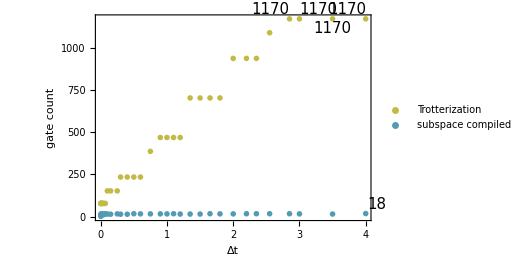

```mathematica
ListPlot[
{datatrotsub,datacompsub},GridLines->None,PlotLegends->Placed[PointLegend[Automatic,{"Trotterization","subspace compiled"},Spacings->0.,LegendFunction->(Framed[#,FrameStyle->(Antialiasing->False),FrameMargins->0]&)],
{0.25,0.8}],FrameLabel->{"Δt","gate count"},ImageSize->Large,PlotMarkers->"OpenMarkers",style]
```

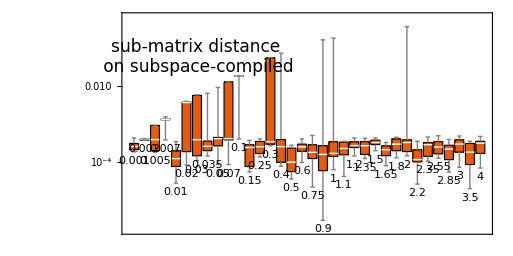

```mathematica
BoxWhiskerChart[Table[subcompsum[t][[All,"distsub"]],{t,times}],ScalingFunctions->"Log2",FrameStyle->Directive[Black,16,FontFamily->"FreeSerif"],Background->White,ChartStyle->Directive[EdgeForm[Black], Automatic],ChartLabels->Placed[times,Below],PlotTheme->"Scientific",Epilog->Text[Style["sub-matrix distance\n on subspace-compiled",17,FontFamily->"FreeSerif",Background->White],Scaled[{.2,.8}]],ImageSize->400,AspectRatio->1/2,
ImagePadding->{{50,10},{37,10}},GridLines->{Range[Length@times],{Log2@(10^-3)}},GridLinesStyle->{GrayLevel[0.1,0.5], Directive[Red,Thick ,Dashed]},ImageSize->Large
]
```

### Trotterizations

```mathematica
stylebig[n_,legends_,legendpos_]:={AspectRatio->1/2,ImageSize->600,
LabelStyle->{FontFamily->"FreeSerif",FontSize->18,Background->None},Frame->True,FrameTicks->Automatic,FrameStyle->Directive[Black,19,FontFamily->"FreeSerif"],
PlotMarkers->"OpenMarkers",Background->White,PlotLegends->Placed[PointLegend[Automatic,legends,Spacings->0.,LegendFunction->(Framed[#,FrameStyle->(Antialiasing->False),FrameMargins->0,Background->White]&)],
legendpos],PlotRange->All,GridLinesStyle->Directive[Black, Dashed]};
```

```mathematica
distidfull<<distidfull.mx;
distidsub<<distidsub.mx;
```

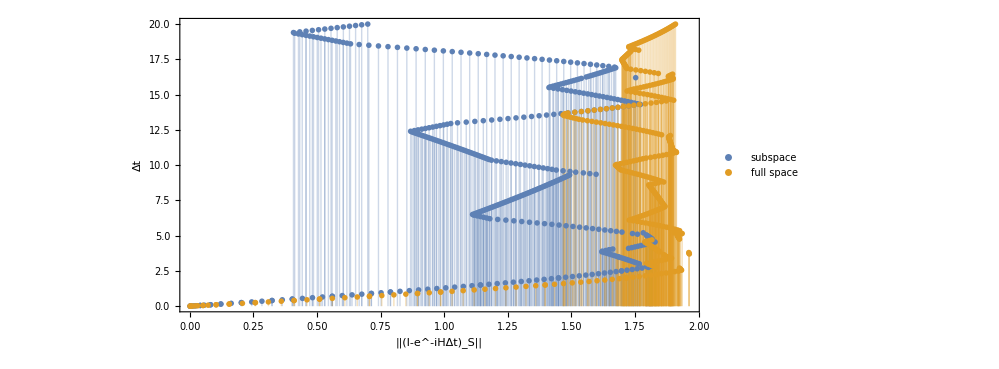

```mathematica
ListPlot[{Transpose@{Values@distidsub,Keys@distidsub},Transpose@{Values@distidfull,Keys@distidfull}},FrameLabel->{TraditionalForm["||(I-e^-iHΔt)_S||"],"Δt"},Filling->Bottom,stylebig[2,{"subspace","full space"},{0.12,0.7}]]
```

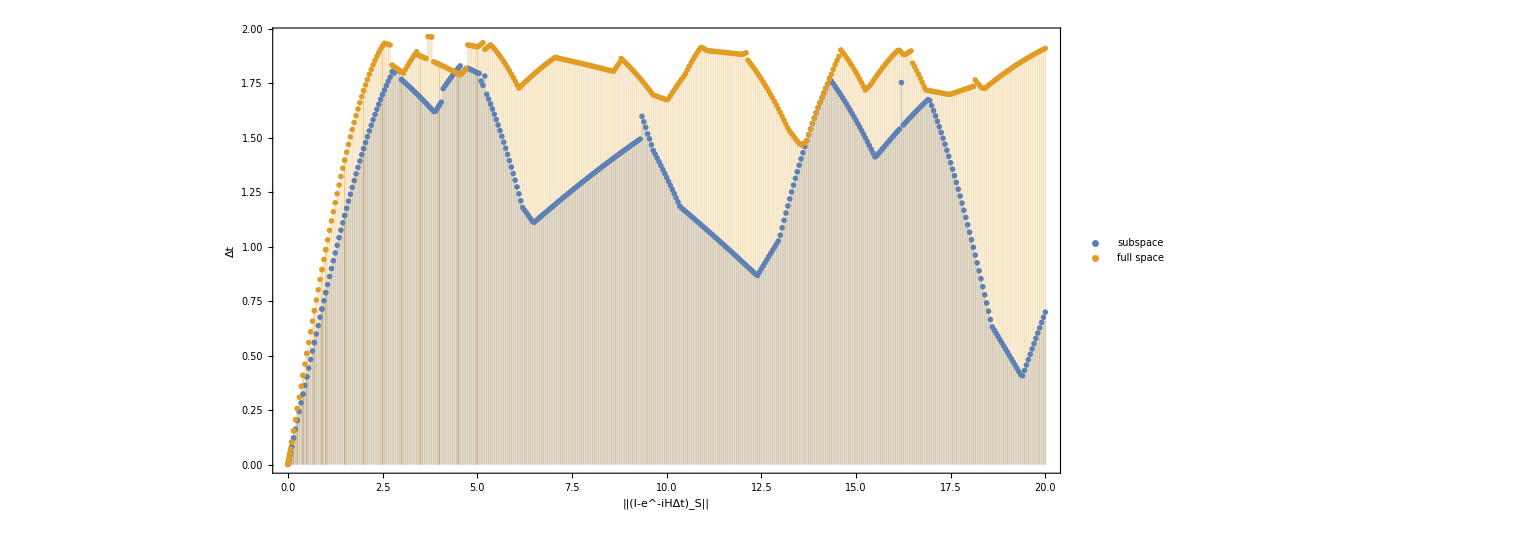

```mathematica
ListPlot[{Transpose@{Keys@distidsub,Values@distidsub},Transpose@{Keys@distidfull,Values@distidfull}},FrameLabel->{TraditionalForm["||(I-e^-iHΔt)_S||"],"Δt"},Filling->Bottom,stylebig[2,{"subspace","full space"},{0.12,0.7}]]
```

### Recompilation results

```mathematica
Directory[]
```

/home/cica/postox/papers/chemistry-code/dynamics

```mathematica
times=Sort@Keys@subcompsum
```

{0.001,0.002,0.005,0.007,0.01,0.02,0.03,0.035,0.05,0.07,0.1,0.15,0.25,0.5,1,2,4}

```mathematica
data=Table[RandomVariate[NormalDistribution[μ,1],10],{μ,{0,3,2,5}},{2}]
```

{{{-0.62805,0.503139,-0.494432,1.3825,0.806005,-1.20586,-1.6322,0.270215,0.57163,-0.858467},{-0.398531,1.46245,0.522917,-0.0665072,-0.269048,0.94427,0.114433,-0.0530903,-0.204544,-0.051371}},{{2.65654,3.20133,2.757,2.5076,3.65194,3.32971,4.1456,1.92531,1.55744,2.69508},{4.4198,1.77036,3.63616,3.56958,4.2051,1.92865,2.51282,1.54148,3.14746,4.16609}},{{3.69844,2.63426,1.45459,2.63781,1.111,1.73925,1.18212,0.801854,3.00952,3.54192},{2.57924,0.327004,1.93919,2.68027,2.03904,3.06969,1.63642,0.950428,3.54201,1.03972}},{{5.19373,5.32771,3.86425,4.31977,5.74075,6.46626,3.85115,5.14925,6.67209,5.87086},{5.28371,5.33527,5.3631,5.41208,4.69648,6.21761,4.94647,4.85357,4.07642,4.41286}}}

```mathematica
subcompsum[1][[1]]
```

<|cost→2.23578×10^-9,distfull→1.7243,distsub→0.0000615311,ansatz→{Rz_0[-3.0801],C_1[Rz_3[-8.73735]],C_3[Ry_1[3.14159]],C_2[Rz_1[-8.3749]],C_1[Rz_3[-9.32908]],C_2[Ry_0[3.14154]],C_2[Rx_3[3.14159]],C_3[Rx_1[-3.14159]],C_3[Ry_2[-0.362331]],C_0[Rx_2[8.97569]],C_1[Ry_2[0.362319]],C_0[Rx_2[-8.96725]],C_2[Rz_3[-3.18653]],C_2[Ry_0[-3.14163]],C_2[Ry_3[3.14159]],C_1[Rz_2[-11.7368]],C_2[Ry_1[3.14159]]},runtime→2.34237|>

```mathematica
color
```

{RGBColor[0.7285450767713475, 0.03494508851712408, 0.14198068147566834],RGBColor[0.4582847199296809, 0.6086754253762674, 0.6585971050832811]}

```mathematica
Around@subcompsum[0.1][[All,"distsub"]]
```

0.0150.008

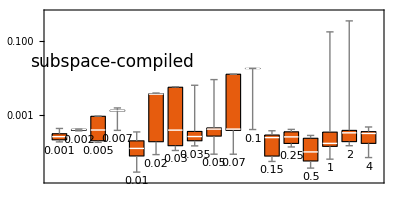

```mathematica
BoxWhiskerChart[Table[subcompsum[t][[All,"distsub"]],{t,times}],ScalingFunctions->"Log2",FrameStyle->Directive[Black,16,FontFamily->"FreeSerif"],Background->White,ChartStyle->Directive[EdgeForm[Black], Automatic],ChartLabels->Placed[times,Below],PlotTheme->"Scientific",Epilog->Text[Style["subspace-compiled",17,FontFamily->"FreeSerif",Background->White],Scaled[{.2,.7}]],ImageSize->400,AspectRatio->1/2,
ImagePadding->{{50,10},{37,10}},GridLines->{Range[Length@times],{Log2@(10^-3)}},GridLinesStyle->{GrayLevel[0.1,0.3], Directive[Red,Thick ,Dashed]}
]
```

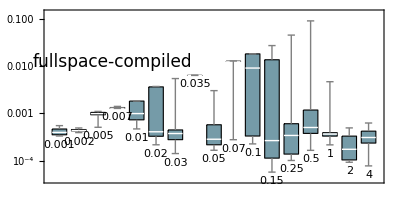

```mathematica
BoxWhiskerChart[Table[fullcompsum[t][[All,"distsub"]],{t,times}],ScalingFunctions->"Log2",FrameStyle->Directive[Black,16,FontFamily->"FreeSerif"],Background->White,ChartStyle->Directive[EdgeForm[Black], color[[2]]],ChartLabels->Placed[times,Below],PlotTheme->"Scientific",Epilog->Text[Style["fullspace-compiled",17,FontFamily->"FreeSerif",Background->White],Scaled[{.2,.7}]],ImageSize->400,ImagePadding->{{50,10},{37,0}},GridLines->{Range[Length@times],{Log2@(10^-3)}},GridLinesStyle->{GrayLevel[0.1,0.3], Directive[Red,Thick ,Dashed]},AspectRatio->1/2
]
```

```mathematica
Directory[]
```

/home/cica/postox/papers/chemistry-code/vqe

```mathematica
subcompsum
```

<|0.001→{<|cost→9.55291×10^-8,distfull→0.232902,distsub→0.00037415,ansatz→{Rx_3[0.00154887],C_2[Rz_3[-0.232746]],Rx_3[-0.00155846],C_0[Rz_3[0.233532]],C_3[Rz_1[0.233399]],C_1[Rz_2[0.000497306]],C_0[Rz_1[0.466841]],Rz_1[-0.350486]},runtime→0.39558|>,8,<|cost→4.99707×10^-8,distfull→0.00123118,distsub→0.000299726,ansatz→{C_1[Rz_3[0.00117034]],C_0[Rz_2[-0.00117723]],Rz_2[0.0015176]},runtime→0.26575|>},0.002→{1},13,2→{<|cost→8.82211×10^-8,3,runtime→2.75748|>,8,<|1|>},4→{1}|>
 |  |  |  |

```mathematica
succompsub=<|Table[t->Select[subcompsum[t],#["distsub"]<=mindist&],{t,Keys@subcompsum}]|>;
succompfull=<|Table[t->Select[fullcompsum[t],#["distsub"]<=mindist&],{t,Keys@fullcompsum}]|>;
```

```mathematica
data
```

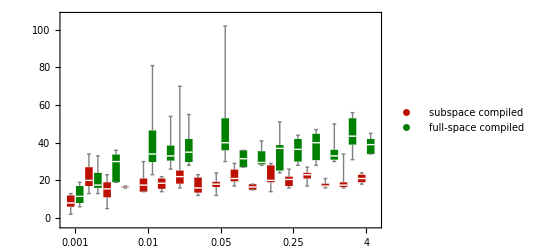

```mathematica
BoxWhiskerChart[Transpose@{Table[Length@#&/@succompsub[t][[All,"ansatz"]],{t,times}],Table[Length@#&/@succompfull[t][[All,"ansatz"]],{t,times}]},FrameStyle->Directive[Black,16,FontFamily->"FreeSerif"],Background->White,ChartStyle->58,ChartLabels->{Placed[times,Axis,Rotate[#,45Degree]&],None},ImageSize->600,ChartLegends->Placed[PointLegend[Automatic,{"subspace compiled","full-space compiled"},Spacings->0.,LegendFunction->(Framed[#,FrameStyle->(Antialiasing->False),FrameMargins->0]&)],
{0.15,0.88}]]
```

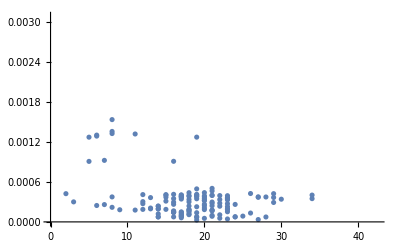

```mathematica
ListPlot[{#[[3]],#[[2]]}&/@Flatten[Values[ressubH2],1]]
```

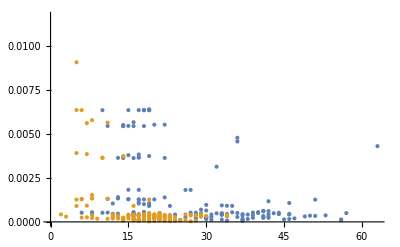

```mathematica
ListPlot[{{#[[3]],#[[2]]}&/@Flatten[Values[resfullH2],1],{#[[3]],#[[2]]}&/@Flatten[Values[ressubH2],1]}]
```